# Lab report 8 – Data processing

Initialise ErrorBarPlots`

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
fontFamily = "Proxima Nova"
```

Proxima Nova

## Data

```mathematica
processedData1 = {
{
{0.0227,0.0667},
ErrorBar[0.0002,0.0004]
}, {
{0.0263,0.0625},
ErrorBar[0.0002,0.0004]
}, {
{0.0294,0.0588},
ErrorBar[0.0003,0.0003]
}, {
{0.0324,0.0556},
ErrorBar[0.0003,0.0003]
}, {
{0.0348,0.0526},
ErrorBar[0.0004,0.0003]
}, {
{0.0373,0.0500},
ErrorBar[0.0004,0.0003]
}, {
{0.0394,0.0476},
ErrorBar[0.0005,0.0002]
}, {
{0.0415,0.0456},
ErrorBar[0.0005,0.0002]
}
}
```

{{{0.0227,0.0667},ErrorBar[0.0002,0.0004]},{{0.0263,0.0625},ErrorBar[0.0002,0.0004]},{{0.0294,0.0588},ErrorBar[0.0003,0.0003]},{{0.0324,0.0556},ErrorBar[0.0003,0.0003]},{{0.0348,0.0526},ErrorBar[0.0004,0.0003]},{{0.0373,0.05},ErrorBar[0.0004,0.0003]},{{0.0394,0.0476},ErrorBar[0.0005,0.0002]},{{0.0415,0.0456},ErrorBar[0.0005,0.0002]}}

```mathematica
processedData2 = {
{
{59.0,660},
ErrorBar[0.2,9]
}, {
{54.1,610},
ErrorBar[0.2,9]
}, {
{51.0,578},
ErrorBar[0.2,9]
}, {
{48.9,556},
ErrorBar[0.2,9]
}, {
{47.7,545},
ErrorBar[0.2,9]
}, {
{46.8,536},
ErrorBar[0.2,9]
}, {
{46.4,533},
ErrorBar[0.2,9]
}, {
{46.1,530},
ErrorBar[0.2,9]
}
}
```

{{{59.,660},ErrorBar[0.2,9]},{{54.1,610},ErrorBar[0.2,9]},{{51.,578},ErrorBar[0.2,9]},{{48.9,556},ErrorBar[0.2,9]},{{47.7,545},ErrorBar[0.2,9]},{{46.8,536},ErrorBar[0.2,9]},{{46.4,533},ErrorBar[0.2,9]},{{46.1,530},ErrorBar[0.2,9]}}

## Linear equation setup

Defining some linear equations for both y-intercept and gradient method

```mathematica
best1[x_]= -1.13x+0.0924
max1[x_]= -1.24x+0.09528
min1[x_]= -1.09x+0.0912 (* Slight adjustment as it missed the error bars; will readjust calculations in the future *)
```

0.0924-1.13 x

0.09528-1.24 x

0.0912-1.09 x

```mathematica
best2[x_]= 10.14x+62
max2[x_] = 11.43x-6
min2[x_]= 8.714x+137
```

62+10.14 x

-6+11.43 x

137+8.714 x

## Plots

Plotting errors for both methods

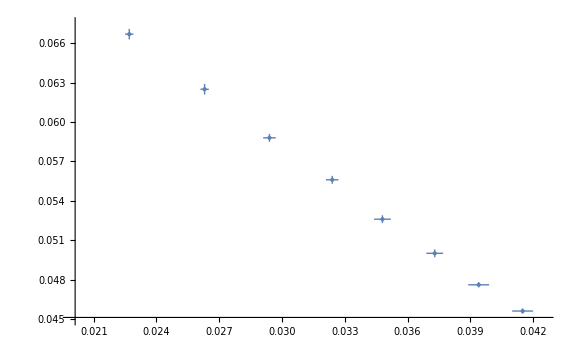

```mathematica
error1 = ErrorListPlot[processedData1,PlotStyle-> {Thickness[Medium], PointSize[Medium]}, ImageSize->Large , PlotRange->{{0.02,0.0425},{0.0450,0.0675}}]
```

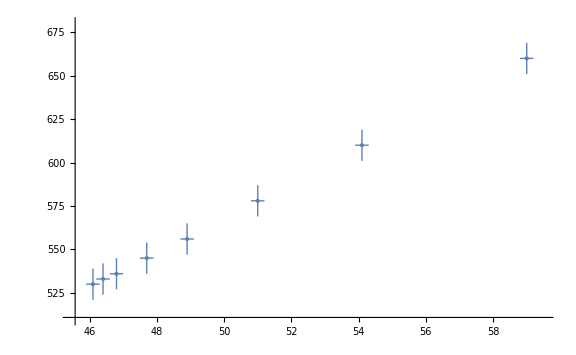

```mathematica
error2 = ErrorListPlot[processedData2,PlotStyle->{Thickness[Medium], PointSize[Medium]}, ImageSize->Large, PlotRange->{{45.5,59.5},{510,680}}]
```

Plot the best, maximum, and minimum lines for both methods.

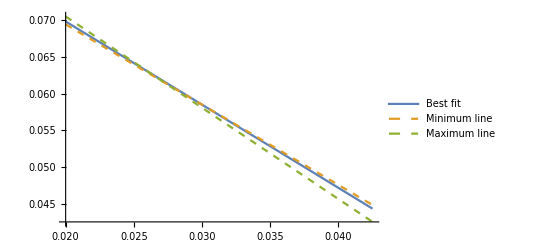

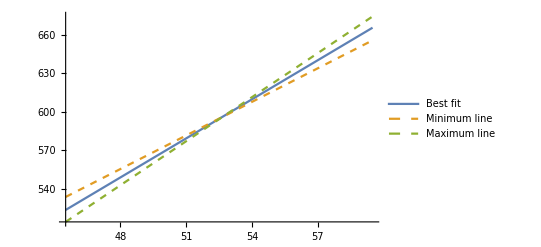

```mathematica
line1 = Plot[{best1[x], min1[x], max1[x]},{x, 0.02,0.0425},PlotStyle->{{Thickness[Medium],Normal}, {Thickness[Medium],Dashed}, {Thickness[Medium],Dashed}}, PlotLegends->{"Best fit", "Minimum line", "Maximum line"},LabelStyle->{FontFamily-> fontFamily, FontWeight->"Light"}]
line2= Plot[{best2[x], min2[x], max2[x]}, {x, 45.5,59.5},PlotStyle->{{Thickness[Medium],Normal}, {Thickness[Medium],Dashed}, {Thickness[Medium],Dashed}}, PlotLegends->{"Best fit", "Minimum line", "Maximum line"}, LabelStyle->{FontFamily-> fontFamily,FontWeight->"Light"}]
```

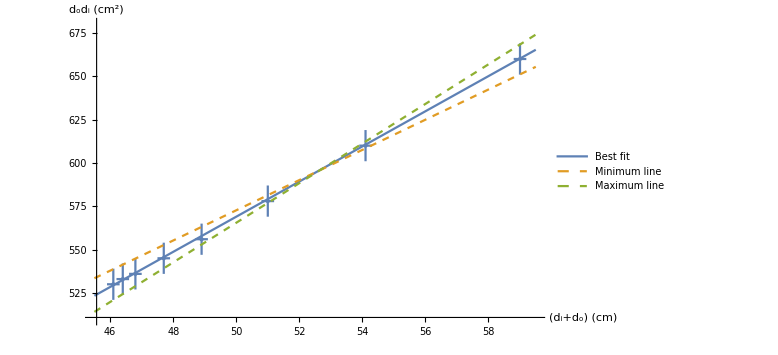

```mathematica
plot1=Show[error2, line2,AxesLabel-> {"(d_i+d_o) (cm)","d_od_i (cm^2)"}, LabelStyle->{FontFamily->fontFamily, FontSize->12, FontWeight->"Light"}]
```

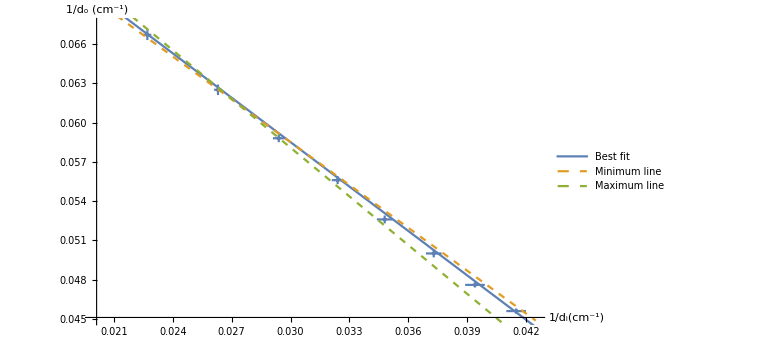

```mathematica
plot2=Show[error1, line1,AxesLabel-> {"1/d_i(cm^-1)","1/d_o (cm^-1)"}, LabelStyle->{FontFamily->fontFamily, FontSize-> 12, FontWeight->"Light"}]
```

```mathematica
Export["~/Documents/GitHub/physics-lab-report-8/images/plot1.pdf", plot1]
Export["~/Documents/GitHub/physics-lab-report-8/images/plot2.pdf", plot2]
```

~/Documents/GitHub/physics-lab-report-8/images/plot1.pdf

~/Documents/GitHub/physics-lab-report-8/images/plot2.pdf